# Kim Polynomial Coefficients Solver

## GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

## General Extrapolation Polynomial

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=4; (*order of the scheme*)
freeInteriorPars=3; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=8; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

(*other info to print?*)
Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
Print["Coefficients:\n",MatrixForm[pCoeffs]]
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40320 | 362880 yHat | 1814400 yHat^2 | 6652800 yHat^3 | 19958400 yHat^4 | 51891840 yHat^5) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fp0
fp1
fp2
fp3
fp4
fp5
0)

Singularities:
(yHat→1.23232
yHat→2.01136
yHat→2.75838
yHat→3.50832
yHat→4.33577)

Coefficients:
(p0→f0
p1→fp0
p2→-(-1858299912 f0-4381542000 f1-1715085000 f2+4814640000 f3+2841165000 f4+297564912 f5+1557000 f6-721229040 fp0-3821580000 fp1-7760340000 fp2-5740560000 fp3-1374030000 fp4-76295520 fp5+4185427743 f0 yHat+10861484400 f1 yHat+5225512500 f2 yHat-11939040000 f3 yHat-7515939375 f4 yHat-813088368 f5 yHat-4356900 f6 yHat+1604579760 fp0 yHat+8972532000 fp1 yHat+19286910000 fp2 yHat+14901840000 fp3 yHat+3684487500 fp4 yHat+209602080 fp5 yHat-3531839850 f0 yHat^2-9873900000 f1 yHat^2-5556600000 f2 yHat^2+10850400000 f3 yHat^2+7290506250 f4 yHat^2+816933600 f5 yHat^2+4500000 f6 yHat^2-1341522000 fp0 yHat^2-7824600000 fp1 yHat^2-17641800000 fp2 yHat^2-14191200000 fp3 yHat^2-3626775000 fp4 yHat^2-211896000 fp5 yHat^2+1410045175 f0 yHat^3+4181760000 f1 yHat^3+2661862500 f2 yHat^3-4584800000 f3 yHat^3-3284634375 f4 yHat^3-382060800 f5 yHat^3-2172500 f6 yHat^3+531762000 fp0 yHat^3+3207600000 fp1 yHat^3+7528950000 fp2 yHat^3+6283200000 fp3 yHat^3+1659487500 fp4 yHat^3+99792000 fp5 yHat^3-268331580 f0 yHat^4-834570000 f1 yHat^4-586575000 f2 yHat^4+910800000 f3 yHat^4+694237500 f4 yHat^4+83944080 f5 yHat^4+495000 f6 yHat^4-100623600 fp0 yHat^4-623700000 fp1 yHat^4-1514700000 fp2 yHat^4-1306800000 fp3 yHat^4-356400000 fp4 yHat^4-22096800 fp5 yHat^4+19582563 f0 yHat^5+63320400 f1 yHat^5+48262500 f2 yHat^5-68640000 f3 yHat^5-55501875 f4 yHat^5-6980688 f5 yHat^5-42900 f6 yHat^5+7310160 fp0 yHat^5+46332000 fp1 yHat^5+115830000 fp2 yHat^5+102960000 fp3 yHat^5+28957500 fp4 yHat^5+1853280 fp5 yHat^5)/(3600 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p3→-(141198373848 f0+569175156000 f1+258599970000 f2-576600480000 f3-354507255000 f4-37666978848 f5-198786000 f6+41316927120 fp0+398108520000 fp1+921273480000 fp2+708081120000 fp3+172525410000 fp4+9677517120 fp5-326046138327 f0 yHat-1426418812800 f1 yHat-774952312500 f2 yHat+1461178080000 f3 yHat+960242394375 f4 yHat+105426893952 f5 yHat+569895300 f6 yHat-94238361630 fp0 yHat-957975984000 fp1 yHat-2343586770000 fp2 yHat-1881895680000 fp3 yHat-473802918750 fp4 yHat-27234506880 fp5 yHat+280033648650 f0 yHat^2+1306400400000 f1 yHat^2+816222825000 f2 yHat^2-1347436800000 f3 yHat^2-946898606250 f4 yHat^2-107722742400 f5 yHat^2-598725000 f6 yHat^2+80190148500 fp0 yHat^2+850111200000 fp1 yHat^2+2178908100000 fp2 yHat^2+1821830400000 fp3 yHat^2+474223612500 fp4 yHat^2+28001376000 fp5 yHat^2-113267436975 f0 yHat^3-556239420000 f1 yHat^3-388657912500 f2 yHat^3+575141600000 f3 yHat^3+431729409375 f4 yHat^3+51001077600 f5 yHat^3+292682500 f6 yHat^3-32202612750 fp0 yHat^3-353014200000 fp1 yHat^3-941029650000 fp2 yHat^3-816314400000 fp3 yHat^3-219637068750 fp4 yHat^3-13350744000 fp5 yHat^3+21769919820 f0 yHat^4+111452220000 f1 yHat^4+85298400000 f2 yHat^4-115077600000 f3 yHat^4-92066287500 f4 yHat^4-11309332320 f5 yHat^4-67320000 f6 yHat^4+6154255800 fp0 yHat^4+69319800000 fp1 yHat^4+191030400000 fp2 yHat^4+171309600000 fp3 yHat^4+47601675000 fp4 yHat^4+2983780800 fp5 yHat^4-1601106507 f0 yHat^5-8481844800 f1 yHat^5-6998062500 f2 yHat^5+8717280000 f3 yHat^5+7410706875 f4 yHat^5+947149632 f5 yHat^5+5877300 f6 yHat^5-450565830 fp0 yHat^5-5189184000 fp1 yHat^5-14710410000 fp2 yHat^5-13590720000 fp3 yHat^5-3894783750 fp4 yHat^5-252046080 fp5 yHat^5)/(108000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p4→-(-1007495377980 f0-5615049854700 f1-3113598998250 f2+5672302428000 f3+3665350435500 f4+396377155980 f5+2114211450 f6-263384912700 fp0-3451433895000 fp1-8994439233000 fp2-7221693492000 fp3-1797584548500 fp4-102096142200 fp5+2416078821807 f0 yHat+14519315835180 f1 yHat+9390676933125 f2 yHat-14872831128000 f3 yHat-10295934127875 f4 yHat-1151016493932 f5 yHat-6289840305 f6 yHat+623864462130 fp0 yHat+8624800895400 fp1 yHat+23723848579500 fp2 yHat+19902953988000 fp3 yHat+5120804306250 fp4 yHat+298109474280 fp5 yHat-2128512055950 f0 yHat^2-13574344095000 f1 yHat^2-9927724095000 f2 yHat^2+14018314680000 f3 yHat^2+10400255313750 f4 yHat^2+1205236762200 f5 yHat^2+6773490000 f6 yHat^2-544503141000 fp0 yHat^2-7850574270000 fp1 yHat^2-22594910310000 fp2 yHat^2-19737338040000 fp3 yHat^2-5251548330000 fp4 yHat^2-314123670000 fp5 yHat^2+876639021335 f0 yHat^3+5863592592000 f1 yHat^3+4738440650625 f2 yHat^3-6072303160000 f3 yHat^3-4822466776875 f4 yHat^3-580532736960 f5 yHat^3-3369590125 f6 yHat^3+222641068650 fp0 yHat^3+3319527420000 fp1 yHat^3+9925786777500 fp2 yHat^3+8994667440000 fp3 yHat^3+2474176691250 fp4 yHat^3+152384522400 fp5 yHat^3-170761793400 f0 yHat^4-1187328928500 f1 yHat^4-1041605358750 f2 yHat^4+1227455460000 f3 yHat^4+1041090435000 f4 yHat^4+130365090900 f5 yHat^4+785094750 f6 yHat^4-43121578500 fp0 yHat^4-660654225000 fp1 yHat^4-2040358815000 fp2 yHat^4-1911129660000 fp3 yHat^4-542968717500 fp4 yHat^4-34491501000 fp5 yHat^4+12688242567 f0 yHat^5+91083229380 f1 yHat^5+85552520625 f2 yHat^5-93655848000 f3 yHat^5-84576652875 f4 yHat^5-11022274692 f5 yHat^5-69217005 f6 yHat^5+3189430530 fp0 yHat^5+49966745400 fp1 yHat^5+158623393500 fp2 yHat^5+153044892000 fp3 yHat^5+44846480250 fp4 yHat^5+2941618680 fp5 yHat^5)/(648000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p5→-(1379741206844 f0+9544927280460 f1+6434798477250 f2-9855478204000 f3-6753920959500 f4-746036420844 f5-4031380210 f6+339749870460 fp0+5391252523800 fp1+15555828717000 fp2+13099218132000 fp3+3343162036500 fp4+192753320760 fp5-3519481873635 f0 yHat-26158832860500 f1 yHat-20163648539250 f2 yHat+27376683408000 f3 yHat+20150475397875 f4 yHat+2302056514260 f5 yHat+12747953250 f6 yHat-855958008150 fp0 yHat-14331168243000 fp1 yHat-43584761718000 fp2 yHat-38344287708000 fp3 yHat-10118302656750 fp4 yHat-598113833400 fp5 yHat+3221455405350 f0 yHat^2+25342087653000 f1 yHat^2+21778726533750 f2 yHat^2-26706444360000 f3 yHat^2-21119389233750 f4 yHat^2-2502181686600 f5 yHat^2-14254311750 f6 yHat^2+776165040000 fp0 yHat^2+13554339930000 fp1 yHat^2+43082737245000 fp2 yHat^2+39456782280000 fp3 yHat^2+10769491485000 fp4 yHat^2+654267618000 fp5 yHat^2-1361427061995 f0 yHat^3-11209947309000 f1 yHat^3-10534274313750 f2 yHat^3+11826785520000 f3 yHat^3+10035922606875 f4 yHat^3+1235668290120 f5 yHat^3+7272267750 f6 yHat^3-325643021550 fp0 yHat^3-5881511790000 fp1 yHat^3-19403556480000 fp2 yHat^3-18430168680000 fp3 yHat^3-5201213613750 fp4 yHat^3-325432522800 fp5 yHat^3+270119352360 f0 yHat^4+2308428054900 f1 yHat^4+2336329091250 f2 yHat^4-2426469540000 f3 yHat^4-2204271135000 f4 yHat^4-282410779860 f5 yHat^4-1725043650 f6 yHat^4+64240614900 fp0 yHat^4+1192384017000 fp1 yHat^4+4059866745000 fp2 yHat^4+3984775740000 fp3 yHat^4+1161569227500 fp4 yHat^4+74974739400 fp5 yHat^4-20347321995 f0 yHat^5-179300335500 f1 yHat^5-193098584250 f2 yHat^5+187057728000 f3 yHat^5+181346182875 f4 yHat^5+24188212620 f5 yHat^5+154118250 f6 yHat^5-4816790550 fp0 yHat^5-91432341000 fp1 yHat^5-319791186000 fp2 yHat^5-323227476000 fp3 yHat^5-97180404750 fp4 yHat^5-6477985800 fp5 yHat^5)/(1296000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p6→-(-224593255596 f0-1810884150900 f1-1449032073750 f2+1918607748000 f3+1405826041500 f4+159201808596 f5+873882150 f6-53320693860 fp0-964026743400 fp1-3029755498200 fp2-2679547960800 fp3-703494917100 fp4-41285634120 fp5+642836072682 f0 yHat+5556592317420 f1 yHat+5008793176125 f2 yHat-5954887296000 f3 yHat-4699537103250 f4 yHat-550698493932 f5 yHat-3098673045 f6 yHat+150727876110 fp0 yHat+2875768936200 fp1 yHat+9515134581300 fp2 yHat+8789086807200 fp3 yHat+2386373776650 fp4 yHat+143624161800 fp5 yHat-626115990600 f0 yHat^2-5718867435000 f1 yHat^2-5685282742500 f2 yHat^2+6156103320000 f3 yHat^2+5234104305000 f4 yHat^2+636373740600 f5 yHat^2+3684802500 f6 yHat^2-145432287000 fp0 yHat^2-2894563350000 fp1 yHat^2-10000085850000 fp2 yHat^2-9612243000000 fp3 yHat^2-2699902125000 fp4 yHat^2-167045166000 fp5 yHat^2+275011547690 f0 yHat^3+2625975363000 f1 yHat^3+2831275280625 f2 yHat^3-2822158240000 f3 yHat^3-2581800251250 f4 yHat^3-326350816440 f5 yHat^3-1952883625 f6 yHat^3+63414547350 fp0 yHat^3+1305559530000 fp1 yHat^3+4677871522500 fp2 yHat^3+4661583960000 fp3 yHat^3+1353899621250 fp4 yHat^3+86292003600 fp5 yHat^3-56006186940 f0 yHat^4-554514295500 f1 yHat^4-639834896250 f2 yHat^4+592021980000 f3 yHat^4+581361907500 f4 yHat^4+76496216940 f5 yHat^4+475274250 f6 yHat^4-12840111900 fp0 yHat^4-271702431000 fp1 yHat^4-1004088393000 fp2 yHat^4-1033570692000 fp3 yHat^4-310069336500 fp4 yHat^4-20391247800 fp5 yHat^4+4298218782 f0 yHat^5+43848167220 f1 yHat^5+53569283625 f2 yHat^5-46325136000 f3 yHat^5-48677235750 f4 yHat^5-6670052532 f5 yHat^5-43245345 f6 yHat^5+980861310 fp0 yHat^5+21228550200 fp1 yHat^5+80545479300 fp2 yHat^5+85350751200 fp3 yHat^5+26407888650 fp4 yHat^5+1793820600 fp5 yHat^5)/(518400 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p7→-(238302217286 f0+2151568334850 f1+1989222445875 f2-2328022954000 f3-1835940810750 f4-213932844786 f5-1196388475 f6+55219101090 fp0+1096740418500 fp1+3701458399500 fp2+3435257262000 fp3+930263991750 fp4+55722260340 fp5-907228103544 f0 yHat-8768795422950 f1 yHat-9033631629750 f2 yHat+9568864296000 f3 yHat+8151744393000 f4 yHat+983407152294 f5 yHat+5639314950 f6 yHat-207613750860 fp0 yHat-4352224810500 fp1 yHat-15449522283000 fp2 yHat-14968704258000 fp3 yHat-4192693204500 fp4 yHat-257625121860 fp5 yHat+991838873550 f0 yHat^2+10119431317500 f1 yHat^2+11403742696875 f2 yHat^2-11055907500000 f3 yHat^2-10177121643750 f4 yHat^2-1274460342300 f5 yHat^2-7523401875 f6 yHat^2+224843123250 fp0 yHat^2+4917742875000 fp1 yHat^2+18213772387500 fp2 yHat^2+18355333500000 fp3 yHat^2+5318969793750 fp4 yHat^2+336072807000 fp5 yHat^2-463710231600 f0 yHat^3-4941994282500 f1 yHat^3-6002370412500 f2 yHat^3+5372076600000 f3 yHat^3+5336656050000 f4 yHat^3+695100044100 f5 yHat^3+4242232500 f6 yHat^3-104353029000 fp0 yHat^3-2361241575000 fp1 yHat^3-9064375650000 fp2 yHat^3-9466092900000 fp3 yHat^3-2836352475000 fp4 yHat^3-184656879000 fp5 yHat^3+98174159490 f0 yHat^4+1084238322750 f1 yHat^4+1402428369375 f2 yHat^4-1166697510000 f3 yHat^4-1247824586250 f4 yHat^4-169245846990 f5 yHat^4-1072908375 f6 yHat^4+21965441850 fp0 yHat^4+510916477500 fp1 yHat^4+2021880217500 fp2 yHat^4+2180165130000 fp3 yHat^4+674703438750 fp4 yHat^4+45331793100 fp5 yHat^4-7735181454 f0 yHat^5-87978483450 f1 yHat^5-120018219750 f2 yHat^5+93343536000 f3 yHat^5+107149506750 f4 yHat^5+15138648954 f5 yHat^5+100192950 f6 yHat^5-1722623760 fp0 yHat^5-40986445500 fp1 yHat^5-166459293000 fp2 yHat^5-184702518000 fp3 yHat^5-58945887000 fp4 yHat^5-4091347260 fp5 yHat^5)/(2592000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p8→-(yHat (45204833898 f0+475777638270 f1+548352811125 f2-524271654000 f3-484346027250 f4-60363664398 f5-353937645 f6+10169453070 fp0+228756239100 fp1+861134692500 fp2+872998290000 fp3+252703010250 fp4+15896073420 fp5-65754240300 f0 yHat-730005952500 f1 yHat-914693073750 f2 yHat+802351620000 f3 yHat+803478217500 f4 yHat+103995465300 f5 yHat+627963750 f6 yHat-14652886500 fp0 yHat-343950705000 fp1 yHat-1350093015000 fp2 yHat-1422937260000 fp3 yHat-426117307500 fp4 yHat-27569565000 fp5 yHat+34515340090 f0 yHat^2+400059486750 f1 yHat^2+537684118125 f2 yHat^2-435770390000 f3 yHat^2-472461701250 f4 yHat^2-63629452590 f5 yHat^2-397401125 f6 yHat^2+7635208350 fp0 yHat^2+185440117500 fp1 yHat^2+754090672500 fp2 yHat^2+823217010000 fp3 yHat^2+254883296250 fp4 yHat^2+16995617100 fp5 yHat^2-7779835800 f0 yHat^3-93406797000 f1 yHat^3-133191877500 f2 yHat^3+100310760000 f3 yHat^3+117479835000 f4 yHat^3+16480945800 f5 yHat^3+106969500 f6 yHat^3-1711017000 fp0 yHat^3-42723450000 fp1 yHat^3-179028630000 fp2 yHat^3-201710520000 fp3 yHat^3-64495035000 fp4 yHat^3-4438962000 fp5 yHat^3+637374738 f0 yHat^4+7878512070 f1 yHat^4+11812568625 f2 yHat^4-8308014000 f3 yHat^4-10478432250 f4 yHat^4-1531625238 f5 yHat^4-10383945 f6 yHat^4+139523670 fp0 yHat^4+3564089100 fp1 yHat^4+15322378500 fp2 yHat^4+17758026000 fp3 yHat^4+5854241250 fp4 yHat^4+416293020 fp5 yHat^4))/(864000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p9→-(-5022759322 f0-52864182030 f1-60928090125 f2+58252406000 f3+53816225250 f4+6707073822 f5+39326405 f6-1129939230 fp0-25417359900 fp1-95681632500 fp2-96999810000 fp3-28078112250 fp4-1766230380 fp5+6909145950 f0 yHat^2+81938871000 f1 yHat^2+112256364375 f2 yHat^2-89789820000 f3 yHat^2-98072673750 f4 yHat^2-13160302200 f5 yHat^2-81585375 f6 yHat^2+1520426250 fp0 yHat^2+37686060000 fp1 yHat^2+155307577500 fp2 yHat^2+170627760000 fp3 yHat^2+52847538750 fp4 yHat^2+3510216000 fp5 yHat^2-4826430840 f0 yHat^3-59736756750 f1 yHat^3-87461508750 f2 yHat^3+64594640000 f3 yHat^3+76654545000 f4 yHat^3+10706824590 f5 yHat^3+68686750 f6 yHat^3-1054307100 fp0 yHat^3-27042592500 fp1 yHat^3-115410735000 fp2 yHat^3-131273010000 fp3 yHat^3-42030202500 fp4 yHat^3-2877722100 fp5 yHat^3+1221669570 f0 yHat^4+15658280550 f1 yHat^4+24251844375 f2 yHat^4-16618470000 f3 yHat^4-21380906250 f4 yHat^4-3111662070 f5 yHat^4-20756175 f6 yHat^4+265315050 fp0 yHat^4+6997171500 fp1 yHat^4+30762517500 fp2 yHat^4+36098370000 fp3 yHat^4+11933088750 fp4 yHat^4+843450300 fp5 yHat^4-106576470 f0 yHat^5-1406047500 f1 yHat^5-2284425000 f2 yHat^5+1458600000 f3 yHat^5+2028633750 f4 yHat^5+307670220 f5 yHat^5+2145000 f6 yHat^5-23037300 fp0 yHat^5-621621000 fp1 yHat^5-2803086000 fp2 yHat^5-3382236000 fp3 yHat^5-1152508500 fp4 yHat^5-84169800 fp5 yHat^5)/(864000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p10→-(876723204 f0+9733412700 f1+12195907650 f2-10698021600 f3-10713042900 f4-1386606204 f5-8372850 f6+195371820 fp0+4586009400 fp1+18001240200 fp2+18972496800 fp3+5681564100 fp4+367594200 fp5-829097514 f0 yHat-9832664520 f1 yHat-13470763725 f2 yHat+10774778400 f3 yHat+11768720850 f4 yHat+1579236264 f5 yHat+9790245 f6 yHat-182451150 fp0 yHat-4522327200 fp1 yHat-18636909300 fp2 yHat-20475331200 fp3 yHat-6341704650 fp4 yHat-421225920 fp5 yHat+209411510 f0 yHat^3+2730964500 f1 yHat^3+4298394375 f2 yHat^3-2906860000 f3 yHat^3-3779448750 f4 yHat^3-548830260 f5 yHat^3-3631375 f6 yHat^3+45310650 fp0 yHat^3+1213245000 fp1 yHat^3+5392777500 fp2 yHat^3+6368340000 fp3 yHat^3+2108328750 fp4 yHat^3+148559400 fp5 yHat^3-70553340 f0 yHat^4-952627500 f1 yHat^4-1582490250 f2 yHat^4+990396000 f3 yHat^4+1401691500 f4 yHat^4+212123340 f5 yHat^4+1460250 f6 yHat^4-15176700 fp0 yHat^4-417879000 fp1 yHat^4-1912977000 fp2 yHat^4-2329668000 fp3 yHat^4-796108500 fp4 yHat^4-57915000 fp5 yHat^4+6912906 f0 yHat^5+96061680 f1 yHat^5+167084775 f2 yHat^5-97125600 f3 yHat^5-149227650 f4 yHat^5-23536656 f5 yHat^5-169455 f6 yHat^5+1480050 fp0 yHat^5+41698800 fp1 yHat^5+195752700 fp2 yHat^5+245044800 fp3 yHat^5+86293350 fp4 yHat^5+6486480 fp5 yHat^5)/(518400 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p11→-(-627551638 f0-7273808850 f1-9776074875 f2+7923098000 f3+8590212750 f4+1156899138 f5+7225475 f6-138821970 fp0-3371638500 fp1-13710739500 fp2-14967582000 fp3-4634241750 fp4-309011220 fp5+789779592 f0 yHat+9775105650 f1 yHat+14311883250 f2 yHat-10570032000 f3 yHat-12543471000 f4 yHat-1752025842 f5 yHat-11239650 f6 yHat+172522980 fp0 yHat+4425151500 fp1 yHat+18885393000 fp2 yHat+21481038000 fp3 yHat+6877669500 fp4 yHat+470899980 fp5 yHat-285561150 f0 yHat^2-3724042500 f1 yHat^2-5861446875 f2 yHat^2+3963900000 f3 yHat^2+5153793750 f4 yHat^2+748404900 f5 yHat^2+4951875 f6 yHat^2-61787250 fp0 yHat^2-1654425000 fp1 yHat^2-7353787500 fp2 yHat^2-8684100000 fp3 yHat^2-2874993750 fp4 yHat^2-202581000 fp5 yHat^2+16714830 f0 yHat^4+235397250 f1 yHat^4+414995625 f2 yHat^4-237930000 f3 yHat^4-370383750 f4 yHat^4-58377330 f5 yHat^4-416625 f6 yHat^4+3568950 fp0 yHat^4+101722500 fp1 yHat^4+481882500 fp2 yHat^4+606870000 fp3 yHat^4+214211250 fp4 yHat^4+16067700 fp5 yHat^4-2180178 f0 yHat^5-31595850 f1 yHat^5-58236750 f2 yHat^5+30888000 f3 yHat^5+52445250 f4 yHat^5+8615178 f5 yHat^5+64350 f6 yHat^5-463320 fp0 yHat^5-13513500 fp1 yHat^5-65637000 fp2 yHat^5-84942000 fp3 yHat^5-30888000 fp4 yHat^5-2393820 fp5 yHat^5)/(2592000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p12→-(47150520 f0+566101800 f1+807223500 f2-607944000 f3-711999000 f4-99884520 f5-648300 f6+10369800 fp0+258930000 fp1+1085022000 fp2+1222488000 fp3+390879000 fp4+26902800 fp5-66636522 f0 yHat-854088030 f1 yHat-1322827875 f2 yHat+906462000 f3 yHat+1166231250 f4 yHat+169727022 f5 yHat+1132155 f6 yHat-14471730 fp0 yHat-381663900 fp1 yHat-1677955500 fp2 yHat-1969002000 fp3 yHat-650895750 fp4 yHat-46006380 fp5 yHat+32069700 f0 yHat^2+433012500 f1 yHat^2+719313750 f2 yHat^2-450180000 f3 yHat^2-637132500 f4 yHat^2-96419700 f5 yHat^2-663750 f6 yHat^2+6898500 fp0 yHat^2+189945000 fp1 yHat^2+869535000 fp2 yHat^2+1058940000 fp3 yHat^2+361867500 fp4 yHat^2+26325000 fp5 yHat^2-5571610 f0 yHat^3-78465750 f1 yHat^3-138331875 f2 yHat^3+79310000 f3 yHat^3+123461250 f4 yHat^3+19459110 f5 yHat^3+138875 f6 yHat^3-1189650 fp0 yHat^3-33907500 fp1 yHat^3-160627500 fp2 yHat^3-202290000 fp3 yHat^3-71403750 fp4 yHat^3-5355900 fp5 yHat^3+60918 f0 yHat^5+913770 f1 yHat^5+1769625 f2 yHat^5-858000 f3 yHat^5-1608750 f4 yHat^5-275418 f5 yHat^5-2145 f6 yHat^5+12870 fp0 yHat^5+386100 fp1 yHat^5+1930500 fp2 yHat^5+2574000 fp3 yHat^5+965250 fp4 yHat^5+77220 fp5 yHat^5)/(2592000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5))
p13→-(-1485722 f0-18364830 f1-27535125 f2+19366000 f3+24425250 f4+3570222 f5+24205 f6-325230 fp0-8307900 fp1-35716500 fp2-41394000 fp3-13646250 fp4-970380 fp5+2235870 f0 yHat+29497500 f1 yHat+47925000 f2 yHat-30600000 f3 yHat-42558750 f4 yHat-6454620 f5 yHat-45000 f6 yHat+483300 fp0 yHat+13041000 fp1 yHat+58806000 fp2 yHat+70956000 fp3 yHat+24178500 fp4 yHat+1765800 fp5 yHat-1208550 f0 yHat^2-16794000 f1 yHat^2-29210625 f2 yHat^2+16980000 f3 yHat^2+26088750 f4 yHat^2+4114800 f5 yHat^2+29625 f6 yHat^2-258750 fp0 yHat^2-7290000 fp1 yHat^2-34222500 fp2 yHat^2-42840000 fp3 yHat^2-15086250 fp4 yHat^2-1134000 fp5 yHat^2+279510 f0 yHat^3+4050750 f1 yHat^3+7466250 f2 yHat^3-3960000 f3 yHat^3-6723750 f4 yHat^3-1104510 f5 yHat^3-8250 f6 yHat^3+59400 fp0 yHat^3+1732500 fp1 yHat^3+8415000 fp2 yHat^3+10890000 fp3 yHat^3+3960000 fp4 yHat^3+306900 fp5 yHat^3-23430 f0 yHat^4-351450 f1 yHat^4-680625 f2 yHat^4+330000 f3 yHat^4+618750 f4 yHat^4+105930 f5 yHat^4+825 f6 yHat^4-4950 fp0 yHat^4-148500 fp1 yHat^4-742500 fp2 yHat^4-990000 fp3 yHat^4-371250 fp4 yHat^4-29700 fp5 yHat^4)/(2592000 (-44616+97569 yHat-80550 yHat^2+31625 yHat^3-5940 yHat^4+429 yHat^5)))

## P4 Extrapolation Polynomial

```mathematica
POrder=13;
fOrder=7;
fpOrder=6;

rowf1={1,0,0,0,0,0,0,0,0,0,0,0,0,0};
rowf=Table[Table[i^j,{j,0,POrder}],{i,1,fOrder-1}];
rowfp1=Transpose@{0,1,0,0,0,0,0,0,0,0,0,0,0,0};
rowfp=Table[Table[j i^(j-1),{j,0,POrder}],{i,1,fpOrder-1}];
rowLast={0,0,0,0,0,0,0,0,8!,(9!)/(1!) y,(10!)/(2!) y^2,(11!)/(3!) y^3,(12!)/(4!) y^4,(13!)/(5!) y^5};


matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowLast];

pVec={p0,p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13};
fVec={f0,f1,f2,f3,f4,f5,f6,fp0,fp1,fp2,fp3,fp4,fp5,0};

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

singularities=(Transpose@Solve[Det[LMat]==0,y])[[1]]//N;

P[x_]=p0+p1 x+p2 x^2+p3 x^3+p4 x^4+p5 x^5+p6 x^6+p7 x^7+p8 x^8+p9 x^9+p10 x^10+p11 x^11+p12 x^12+p13 x^13/.pCoeffs;


Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[singularities]]
Print["Coefficients:\n",MatrixForm[pCoeffs]]
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40320 | 362880 y | 1814400 y^2 | 6652800 y^3 | 19958400 y^4 | 51891840 y^5) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fp0
fp1
fp2
fp3
fp4
fp5
0)

Singularities:
(y→1.23232
y→2.01136
y→2.75838
y→3.50832
y→4.33577)

Coefficients:
(p0→f0
p1→fp0
p2→-(-1858299912 f0-4381542000 f1-1715085000 f2+4814640000 f3+2841165000 f4+297564912 f5+1557000 f6-721229040 fp0-3821580000 fp1-7760340000 fp2-5740560000 fp3-1374030000 fp4-76295520 fp5+4185427743 f0 y+10861484400 f1 y+5225512500 f2 y-11939040000 f3 y-7515939375 f4 y-813088368 f5 y-4356900 f6 y+1604579760 fp0 y+8972532000 fp1 y+19286910000 fp2 y+14901840000 fp3 y+3684487500 fp4 y+209602080 fp5 y-3531839850 f0 y^2-9873900000 f1 y^2-5556600000 f2 y^2+10850400000 f3 y^2+7290506250 f4 y^2+816933600 f5 y^2+4500000 f6 y^2-1341522000 fp0 y^2-7824600000 fp1 y^2-17641800000 fp2 y^2-14191200000 fp3 y^2-3626775000 fp4 y^2-211896000 fp5 y^2+1410045175 f0 y^3+4181760000 f1 y^3+2661862500 f2 y^3-4584800000 f3 y^3-3284634375 f4 y^3-382060800 f5 y^3-2172500 f6 y^3+531762000 fp0 y^3+3207600000 fp1 y^3+7528950000 fp2 y^3+6283200000 fp3 y^3+1659487500 fp4 y^3+99792000 fp5 y^3-268331580 f0 y^4-834570000 f1 y^4-586575000 f2 y^4+910800000 f3 y^4+694237500 f4 y^4+83944080 f5 y^4+495000 f6 y^4-100623600 fp0 y^4-623700000 fp1 y^4-1514700000 fp2 y^4-1306800000 fp3 y^4-356400000 fp4 y^4-22096800 fp5 y^4+19582563 f0 y^5+63320400 f1 y^5+48262500 f2 y^5-68640000 f3 y^5-55501875 f4 y^5-6980688 f5 y^5-42900 f6 y^5+7310160 fp0 y^5+46332000 fp1 y^5+115830000 fp2 y^5+102960000 fp3 y^5+28957500 fp4 y^5+1853280 fp5 y^5)/(3600 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p3→-(141198373848 f0+569175156000 f1+258599970000 f2-576600480000 f3-354507255000 f4-37666978848 f5-198786000 f6+41316927120 fp0+398108520000 fp1+921273480000 fp2+708081120000 fp3+172525410000 fp4+9677517120 fp5-326046138327 f0 y-1426418812800 f1 y-774952312500 f2 y+1461178080000 f3 y+960242394375 f4 y+105426893952 f5 y+569895300 f6 y-94238361630 fp0 y-957975984000 fp1 y-2343586770000 fp2 y-1881895680000 fp3 y-473802918750 fp4 y-27234506880 fp5 y+280033648650 f0 y^2+1306400400000 f1 y^2+816222825000 f2 y^2-1347436800000 f3 y^2-946898606250 f4 y^2-107722742400 f5 y^2-598725000 f6 y^2+80190148500 fp0 y^2+850111200000 fp1 y^2+2178908100000 fp2 y^2+1821830400000 fp3 y^2+474223612500 fp4 y^2+28001376000 fp5 y^2-113267436975 f0 y^3-556239420000 f1 y^3-388657912500 f2 y^3+575141600000 f3 y^3+431729409375 f4 y^3+51001077600 f5 y^3+292682500 f6 y^3-32202612750 fp0 y^3-353014200000 fp1 y^3-941029650000 fp2 y^3-816314400000 fp3 y^3-219637068750 fp4 y^3-13350744000 fp5 y^3+21769919820 f0 y^4+111452220000 f1 y^4+85298400000 f2 y^4-115077600000 f3 y^4-92066287500 f4 y^4-11309332320 f5 y^4-67320000 f6 y^4+6154255800 fp0 y^4+69319800000 fp1 y^4+191030400000 fp2 y^4+171309600000 fp3 y^4+47601675000 fp4 y^4+2983780800 fp5 y^4-1601106507 f0 y^5-8481844800 f1 y^5-6998062500 f2 y^5+8717280000 f3 y^5+7410706875 f4 y^5+947149632 f5 y^5+5877300 f6 y^5-450565830 fp0 y^5-5189184000 fp1 y^5-14710410000 fp2 y^5-13590720000 fp3 y^5-3894783750 fp4 y^5-252046080 fp5 y^5)/(108000 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p4→-(-1007495377980 f0-5615049854700 f1-3113598998250 f2+5672302428000 f3+3665350435500 f4+396377155980 f5+2114211450 f6-263384912700 fp0-3451433895000 fp1-8994439233000 fp2-7221693492000 fp3-1797584548500 fp4-102096142200 fp5+2416078821807 f0 y+14519315835180 f1 y+9390676933125 f2 y-14872831128000 f3 y-10295934127875 f4 y-1151016493932 f5 y-6289840305 f6 y+623864462130 fp0 y+8624800895400 fp1 y+23723848579500 fp2 y+19902953988000 fp3 y+5120804306250 fp4 y+298109474280 fp5 y-2128512055950 f0 y^2-13574344095000 f1 y^2-9927724095000 f2 y^2+14018314680000 f3 y^2+10400255313750 f4 y^2+1205236762200 f5 y^2+6773490000 f6 y^2-544503141000 fp0 y^2-7850574270000 fp1 y^2-22594910310000 fp2 y^2-19737338040000 fp3 y^2-5251548330000 fp4 y^2-314123670000 fp5 y^2+876639021335 f0 y^3+5863592592000 f1 y^3+4738440650625 f2 y^3-6072303160000 f3 y^3-4822466776875 f4 y^3-580532736960 f5 y^3-3369590125 f6 y^3+222641068650 fp0 y^3+3319527420000 fp1 y^3+9925786777500 fp2 y^3+8994667440000 fp3 y^3+2474176691250 fp4 y^3+152384522400 fp5 y^3-170761793400 f0 y^4-1187328928500 f1 y^4-1041605358750 f2 y^4+1227455460000 f3 y^4+1041090435000 f4 y^4+130365090900 f5 y^4+785094750 f6 y^4-43121578500 fp0 y^4-660654225000 fp1 y^4-2040358815000 fp2 y^4-1911129660000 fp3 y^4-542968717500 fp4 y^4-34491501000 fp5 y^4+12688242567 f0 y^5+91083229380 f1 y^5+85552520625 f2 y^5-93655848000 f3 y^5-84576652875 f4 y^5-11022274692 f5 y^5-69217005 f6 y^5+3189430530 fp0 y^5+49966745400 fp1 y^5+158623393500 fp2 y^5+153044892000 fp3 y^5+44846480250 fp4 y^5+2941618680 fp5 y^5)/(648000 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p5→-(1379741206844 f0+9544927280460 f1+6434798477250 f2-9855478204000 f3-6753920959500 f4-746036420844 f5-4031380210 f6+339749870460 fp0+5391252523800 fp1+15555828717000 fp2+13099218132000 fp3+3343162036500 fp4+192753320760 fp5-3519481873635 f0 y-26158832860500 f1 y-20163648539250 f2 y+27376683408000 f3 y+20150475397875 f4 y+2302056514260 f5 y+12747953250 f6 y-855958008150 fp0 y-14331168243000 fp1 y-43584761718000 fp2 y-38344287708000 fp3 y-10118302656750 fp4 y-598113833400 fp5 y+3221455405350 f0 y^2+25342087653000 f1 y^2+21778726533750 f2 y^2-26706444360000 f3 y^2-21119389233750 f4 y^2-2502181686600 f5 y^2-14254311750 f6 y^2+776165040000 fp0 y^2+13554339930000 fp1 y^2+43082737245000 fp2 y^2+39456782280000 fp3 y^2+10769491485000 fp4 y^2+654267618000 fp5 y^2-1361427061995 f0 y^3-11209947309000 f1 y^3-10534274313750 f2 y^3+11826785520000 f3 y^3+10035922606875 f4 y^3+1235668290120 f5 y^3+7272267750 f6 y^3-325643021550 fp0 y^3-5881511790000 fp1 y^3-19403556480000 fp2 y^3-18430168680000 fp3 y^3-5201213613750 fp4 y^3-325432522800 fp5 y^3+270119352360 f0 y^4+2308428054900 f1 y^4+2336329091250 f2 y^4-2426469540000 f3 y^4-2204271135000 f4 y^4-282410779860 f5 y^4-1725043650 f6 y^4+64240614900 fp0 y^4+1192384017000 fp1 y^4+4059866745000 fp2 y^4+3984775740000 fp3 y^4+1161569227500 fp4 y^4+74974739400 fp5 y^4-20347321995 f0 y^5-179300335500 f1 y^5-193098584250 f2 y^5+187057728000 f3 y^5+181346182875 f4 y^5+24188212620 f5 y^5+154118250 f6 y^5-4816790550 fp0 y^5-91432341000 fp1 y^5-319791186000 fp2 y^5-323227476000 fp3 y^5-97180404750 fp4 y^5-6477985800 fp5 y^5)/(1296000 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p6→-(-224593255596 f0-1810884150900 f1-1449032073750 f2+1918607748000 f3+1405826041500 f4+159201808596 f5+873882150 f6-53320693860 fp0-964026743400 fp1-3029755498200 fp2-2679547960800 fp3-703494917100 fp4-41285634120 fp5+642836072682 f0 y+5556592317420 f1 y+5008793176125 f2 y-5954887296000 f3 y-4699537103250 f4 y-550698493932 f5 y-3098673045 f6 y+150727876110 fp0 y+2875768936200 fp1 y+9515134581300 fp2 y+8789086807200 fp3 y+2386373776650 fp4 y+143624161800 fp5 y-626115990600 f0 y^2-5718867435000 f1 y^2-5685282742500 f2 y^2+6156103320000 f3 y^2+5234104305000 f4 y^2+636373740600 f5 y^2+3684802500 f6 y^2-145432287000 fp0 y^2-2894563350000 fp1 y^2-10000085850000 fp2 y^2-9612243000000 fp3 y^2-2699902125000 fp4 y^2-167045166000 fp5 y^2+275011547690 f0 y^3+2625975363000 f1 y^3+2831275280625 f2 y^3-2822158240000 f3 y^3-2581800251250 f4 y^3-326350816440 f5 y^3-1952883625 f6 y^3+63414547350 fp0 y^3+1305559530000 fp1 y^3+4677871522500 fp2 y^3+4661583960000 fp3 y^3+1353899621250 fp4 y^3+86292003600 fp5 y^3-56006186940 f0 y^4-554514295500 f1 y^4-639834896250 f2 y^4+592021980000 f3 y^4+581361907500 f4 y^4+76496216940 f5 y^4+475274250 f6 y^4-12840111900 fp0 y^4-271702431000 fp1 y^4-1004088393000 fp2 y^4-1033570692000 fp3 y^4-310069336500 fp4 y^4-20391247800 fp5 y^4+4298218782 f0 y^5+43848167220 f1 y^5+53569283625 f2 y^5-46325136000 f3 y^5-48677235750 f4 y^5-6670052532 f5 y^5-43245345 f6 y^5+980861310 fp0 y^5+21228550200 fp1 y^5+80545479300 fp2 y^5+85350751200 fp3 y^5+26407888650 fp4 y^5+1793820600 fp5 y^5)/(518400 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p7→-(238302217286 f0+2151568334850 f1+1989222445875 f2-2328022954000 f3-1835940810750 f4-213932844786 f5-1196388475 f6+55219101090 fp0+1096740418500 fp1+3701458399500 fp2+3435257262000 fp3+930263991750 fp4+55722260340 fp5-907228103544 f0 y-8768795422950 f1 y-9033631629750 f2 y+9568864296000 f3 y+8151744393000 f4 y+983407152294 f5 y+5639314950 f6 y-207613750860 fp0 y-4352224810500 fp1 y-15449522283000 fp2 y-14968704258000 fp3 y-4192693204500 fp4 y-257625121860 fp5 y+991838873550 f0 y^2+10119431317500 f1 y^2+11403742696875 f2 y^2-11055907500000 f3 y^2-10177121643750 f4 y^2-1274460342300 f5 y^2-7523401875 f6 y^2+224843123250 fp0 y^2+4917742875000 fp1 y^2+18213772387500 fp2 y^2+18355333500000 fp3 y^2+5318969793750 fp4 y^2+336072807000 fp5 y^2-463710231600 f0 y^3-4941994282500 f1 y^3-6002370412500 f2 y^3+5372076600000 f3 y^3+5336656050000 f4 y^3+695100044100 f5 y^3+4242232500 f6 y^3-104353029000 fp0 y^3-2361241575000 fp1 y^3-9064375650000 fp2 y^3-9466092900000 fp3 y^3-2836352475000 fp4 y^3-184656879000 fp5 y^3+98174159490 f0 y^4+1084238322750 f1 y^4+1402428369375 f2 y^4-1166697510000 f3 y^4-1247824586250 f4 y^4-169245846990 f5 y^4-1072908375 f6 y^4+21965441850 fp0 y^4+510916477500 fp1 y^4+2021880217500 fp2 y^4+2180165130000 fp3 y^4+674703438750 fp4 y^4+45331793100 fp5 y^4-7735181454 f0 y^5-87978483450 f1 y^5-120018219750 f2 y^5+93343536000 f3 y^5+107149506750 f4 y^5+15138648954 f5 y^5+100192950 f6 y^5-1722623760 fp0 y^5-40986445500 fp1 y^5-166459293000 fp2 y^5-184702518000 fp3 y^5-58945887000 fp4 y^5-4091347260 fp5 y^5)/(2592000 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p8→-(y (45204833898 f0+475777638270 f1+548352811125 f2-524271654000 f3-484346027250 f4-60363664398 f5-353937645 f6+10169453070 fp0+228756239100 fp1+861134692500 fp2+872998290000 fp3+252703010250 fp4+15896073420 fp5-65754240300 f0 y-730005952500 f1 y-914693073750 f2 y+802351620000 f3 y+803478217500 f4 y+103995465300 f5 y+627963750 f6 y-14652886500 fp0 y-343950705000 fp1 y-1350093015000 fp2 y-1422937260000 fp3 y-426117307500 fp4 y-27569565000 fp5 y+34515340090 f0 y^2+400059486750 f1 y^2+537684118125 f2 y^2-435770390000 f3 y^2-472461701250 f4 y^2-63629452590 f5 y^2-397401125 f6 y^2+7635208350 fp0 y^2+185440117500 fp1 y^2+754090672500 fp2 y^2+823217010000 fp3 y^2+254883296250 fp4 y^2+16995617100 fp5 y^2-7779835800 f0 y^3-93406797000 f1 y^3-133191877500 f2 y^3+100310760000 f3 y^3+117479835000 f4 y^3+16480945800 f5 y^3+106969500 f6 y^3-1711017000 fp0 y^3-42723450000 fp1 y^3-179028630000 fp2 y^3-201710520000 fp3 y^3-64495035000 fp4 y^3-4438962000 fp5 y^3+637374738 f0 y^4+7878512070 f1 y^4+11812568625 f2 y^4-8308014000 f3 y^4-10478432250 f4 y^4-1531625238 f5 y^4-10383945 f6 y^4+139523670 fp0 y^4+3564089100 fp1 y^4+15322378500 fp2 y^4+17758026000 fp3 y^4+5854241250 fp4 y^4+416293020 fp5 y^4))/(864000 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p9→-(-5022759322 f0-52864182030 f1-60928090125 f2+58252406000 f3+53816225250 f4+6707073822 f5+39326405 f6-1129939230 fp0-25417359900 fp1-95681632500 fp2-96999810000 fp3-28078112250 fp4-1766230380 fp5+6909145950 f0 y^2+81938871000 f1 y^2+112256364375 f2 y^2-89789820000 f3 y^2-98072673750 f4 y^2-13160302200 f5 y^2-81585375 f6 y^2+1520426250 fp0 y^2+37686060000 fp1 y^2+155307577500 fp2 y^2+170627760000 fp3 y^2+52847538750 fp4 y^2+3510216000 fp5 y^2-4826430840 f0 y^3-59736756750 f1 y^3-87461508750 f2 y^3+64594640000 f3 y^3+76654545000 f4 y^3+10706824590 f5 y^3+68686750 f6 y^3-1054307100 fp0 y^3-27042592500 fp1 y^3-115410735000 fp2 y^3-131273010000 fp3 y^3-42030202500 fp4 y^3-2877722100 fp5 y^3+1221669570 f0 y^4+15658280550 f1 y^4+24251844375 f2 y^4-16618470000 f3 y^4-21380906250 f4 y^4-3111662070 f5 y^4-20756175 f6 y^4+265315050 fp0 y^4+6997171500 fp1 y^4+30762517500 fp2 y^4+36098370000 fp3 y^4+11933088750 fp4 y^4+843450300 fp5 y^4-106576470 f0 y^5-1406047500 f1 y^5-2284425000 f2 y^5+1458600000 f3 y^5+2028633750 f4 y^5+307670220 f5 y^5+2145000 f6 y^5-23037300 fp0 y^5-621621000 fp1 y^5-2803086000 fp2 y^5-3382236000 fp3 y^5-1152508500 fp4 y^5-84169800 fp5 y^5)/(864000 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p10→-(876723204 f0+9733412700 f1+12195907650 f2-10698021600 f3-10713042900 f4-1386606204 f5-8372850 f6+195371820 fp0+4586009400 fp1+18001240200 fp2+18972496800 fp3+5681564100 fp4+367594200 fp5-829097514 f0 y-9832664520 f1 y-13470763725 f2 y+10774778400 f3 y+11768720850 f4 y+1579236264 f5 y+9790245 f6 y-182451150 fp0 y-4522327200 fp1 y-18636909300 fp2 y-20475331200 fp3 y-6341704650 fp4 y-421225920 fp5 y+209411510 f0 y^3+2730964500 f1 y^3+4298394375 f2 y^3-2906860000 f3 y^3-3779448750 f4 y^3-548830260 f5 y^3-3631375 f6 y^3+45310650 fp0 y^3+1213245000 fp1 y^3+5392777500 fp2 y^3+6368340000 fp3 y^3+2108328750 fp4 y^3+148559400 fp5 y^3-70553340 f0 y^4-952627500 f1 y^4-1582490250 f2 y^4+990396000 f3 y^4+1401691500 f4 y^4+212123340 f5 y^4+1460250 f6 y^4-15176700 fp0 y^4-417879000 fp1 y^4-1912977000 fp2 y^4-2329668000 fp3 y^4-796108500 fp4 y^4-57915000 fp5 y^4+6912906 f0 y^5+96061680 f1 y^5+167084775 f2 y^5-97125600 f3 y^5-149227650 f4 y^5-23536656 f5 y^5-169455 f6 y^5+1480050 fp0 y^5+41698800 fp1 y^5+195752700 fp2 y^5+245044800 fp3 y^5+86293350 fp4 y^5+6486480 fp5 y^5)/(518400 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p11→-(-627551638 f0-7273808850 f1-9776074875 f2+7923098000 f3+8590212750 f4+1156899138 f5+7225475 f6-138821970 fp0-3371638500 fp1-13710739500 fp2-14967582000 fp3-4634241750 fp4-309011220 fp5+789779592 f0 y+9775105650 f1 y+14311883250 f2 y-10570032000 f3 y-12543471000 f4 y-1752025842 f5 y-11239650 f6 y+172522980 fp0 y+4425151500 fp1 y+18885393000 fp2 y+21481038000 fp3 y+6877669500 fp4 y+470899980 fp5 y-285561150 f0 y^2-3724042500 f1 y^2-5861446875 f2 y^2+3963900000 f3 y^2+5153793750 f4 y^2+748404900 f5 y^2+4951875 f6 y^2-61787250 fp0 y^2-1654425000 fp1 y^2-7353787500 fp2 y^2-8684100000 fp3 y^2-2874993750 fp4 y^2-202581000 fp5 y^2+16714830 f0 y^4+235397250 f1 y^4+414995625 f2 y^4-237930000 f3 y^4-370383750 f4 y^4-58377330 f5 y^4-416625 f6 y^4+3568950 fp0 y^4+101722500 fp1 y^4+481882500 fp2 y^4+606870000 fp3 y^4+214211250 fp4 y^4+16067700 fp5 y^4-2180178 f0 y^5-31595850 f1 y^5-58236750 f2 y^5+30888000 f3 y^5+52445250 f4 y^5+8615178 f5 y^5+64350 f6 y^5-463320 fp0 y^5-13513500 fp1 y^5-65637000 fp2 y^5-84942000 fp3 y^5-30888000 fp4 y^5-2393820 fp5 y^5)/(2592000 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p12→-(47150520 f0+566101800 f1+807223500 f2-607944000 f3-711999000 f4-99884520 f5-648300 f6+10369800 fp0+258930000 fp1+1085022000 fp2+1222488000 fp3+390879000 fp4+26902800 fp5-66636522 f0 y-854088030 f1 y-1322827875 f2 y+906462000 f3 y+1166231250 f4 y+169727022 f5 y+1132155 f6 y-14471730 fp0 y-381663900 fp1 y-1677955500 fp2 y-1969002000 fp3 y-650895750 fp4 y-46006380 fp5 y+32069700 f0 y^2+433012500 f1 y^2+719313750 f2 y^2-450180000 f3 y^2-637132500 f4 y^2-96419700 f5 y^2-663750 f6 y^2+6898500 fp0 y^2+189945000 fp1 y^2+869535000 fp2 y^2+1058940000 fp3 y^2+361867500 fp4 y^2+26325000 fp5 y^2-5571610 f0 y^3-78465750 f1 y^3-138331875 f2 y^3+79310000 f3 y^3+123461250 f4 y^3+19459110 f5 y^3+138875 f6 y^3-1189650 fp0 y^3-33907500 fp1 y^3-160627500 fp2 y^3-202290000 fp3 y^3-71403750 fp4 y^3-5355900 fp5 y^3+60918 f0 y^5+913770 f1 y^5+1769625 f2 y^5-858000 f3 y^5-1608750 f4 y^5-275418 f5 y^5-2145 f6 y^5+12870 fp0 y^5+386100 fp1 y^5+1930500 fp2 y^5+2574000 fp3 y^5+965250 fp4 y^5+77220 fp5 y^5)/(2592000 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5))
p13→-(-1485722 f0-18364830 f1-27535125 f2+19366000 f3+24425250 f4+3570222 f5+24205 f6-325230 fp0-8307900 fp1-35716500 fp2-41394000 fp3-13646250 fp4-970380 fp5+2235870 f0 y+29497500 f1 y+47925000 f2 y-30600000 f3 y-42558750 f4 y-6454620 f5 y-45000 f6 y+483300 fp0 y+13041000 fp1 y+58806000 fp2 y+70956000 fp3 y+24178500 fp4 y+1765800 fp5 y-1208550 f0 y^2-16794000 f1 y^2-29210625 f2 y^2+16980000 f3 y^2+26088750 f4 y^2+4114800 f5 y^2+29625 f6 y^2-258750 fp0 y^2-7290000 fp1 y^2-34222500 fp2 y^2-42840000 fp3 y^2-15086250 fp4 y^2-1134000 fp5 y^2+279510 f0 y^3+4050750 f1 y^3+7466250 f2 y^3-3960000 f3 y^3-6723750 f4 y^3-1104510 f5 y^3-8250 f6 y^3+59400 fp0 y^3+1732500 fp1 y^3+8415000 fp2 y^3+10890000 fp3 y^3+3960000 fp4 y^3+306900 fp5 y^3-23430 f0 y^4-351450 f1 y^4-680625 f2 y^4+330000 f3 y^4+618750 f4 y^4+105930 f5 y^4+825 f6 y^4-4950 fp0 y^4-148500 fp1 y^4-742500 fp2 y^4-990000 fp3 y^4-371250 fp4 y^4-29700 fp5 y^4)/(2592000 (-44616+97569 y-80550 y^2+31625 y^3-5940 y^4+429 y^5)))

## Solve for Boundary Coefficients

### Node 2

```mathematica
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]

scheme0=β fp0+α fp1+fp2+α fp3+β fp4-(-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5); (*==0*)
schemefp5=Solve[β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6,fp5][[1]];
scheme0=scheme0/.schemefp5;
schemebd=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)

fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars2];

coeffEqs2={};
For[i=1,i<=Length[fVars2],i++,
AppendTo[coeffEqs2,Coefficient[eq,fVars2[[i]]]==0]]

bdCoeffs2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};


coeffEqs2;

bdCoeffs2=Solve[coeffEqs2,bdCoeffs2][[1]];
γ22=γ22/.bdCoeffs2[[3]];
γ20=γ20/γ22/.bdCoeffs2[[1]];
γ21=γ21/γ22/.bdCoeffs2[[2]];
γ23=γ23/γ22/.bdCoeffs2[[4]];
γ24=γ24/γ22/.bdCoeffs2[[5]];
a20=a20/γ22/.bdCoeffs2[[6]];
a21=a21/γ22/.bdCoeffs2[[7]];
a22=a22/γ22/.bdCoeffs2[[8]];
a23=a23/γ22/.bdCoeffs2[[9]];
a24=a24/γ22/.bdCoeffs2[[10]];
a25=a25/γ22/.bdCoeffs2[[11]];
a26=a26/γ22/.bdCoeffs2[[12]];
gamma20=γ20/.bdCoeffs2[[1]]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392(*,yHat->0.779*)};
```

### Node 1

```mathematica
scheme0=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4); (*==0*)
schemefp5=Solve[β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6,fp5][[1]];
schemefp4=Solve[γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6,fp4][[1]];
scheme0=scheme0/.schemefp5;
scheme0=scheme0/.schemefp4/.bdCoeffs2;
schemebd=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)

fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars1];

coeffEqs1={};
For[i=1,i<=Length[fVars1],i++,
AppendTo[coeffEqs1,Coefficient[eq,fVars1[[i]]]==0]]

bdCoeffs1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};

coeffEqs1;

bdCoeffs1=Solve[coeffEqs1,bdCoeffs1][[1]];
```

### Node 0

```mathematica
scheme0=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3); (*==0*)
schemefp5=Solve[β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6,fp5][[1]];
schemefp4=Solve[γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6,fp4][[1]];
schemefp3=Solve[γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6][[1]];
scheme0=scheme0/.schemefp5;
scheme0=scheme0/.schemefp4/.bdCoeffs2;
scheme0=scheme0/.schemefp3/.bdCoeffs1;
schemebd=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)

fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars0];

coeffEqs0={};
For[i=1,i<=Length[fVars0],i++,
AppendTo[coeffEqs0,Coefficient[eq,fVars0[[i]]]==0]]

bdCoeffs0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};

coeffEqs0;

bdCoeffs0=Solve[coeffEqs0,bdCoeffs0][[1]];

(*Collect[γ00/.bdCoeffs0[[1]]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392(*,yHat->0.779*)},yHat]
γ00/.bdCoeffs0[[1]]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->0.779}*)
```

## Optimize ŷ

Question: Would we have different ŷ values for each node, since each node produces its own spectral function to optimize over?

### Node 2

```mathematica
𝔸[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBarRe[κ_]=(𝔸[κ]*𝔻[κ]-𝔹[κ]*ℂ[κ])/((𝔸[κ])^2+(𝔹[κ])^2);
κBarIm[κ_]=(-𝔸[κ]*ℂ[κ]-𝔹[κ]*𝔻[κ])/((𝔸[κ])^2+(𝔹[κ])^2);
κBarNorm[κ_]=Abs[κBarRe[κ]+I*κBarIm[κ]];


(*ParallelMap[FullSimplify,Assuming[{α∈Reals,β∈Reals,a1∈Reals,a2∈Reals,a3∈Reals,yHat∈Reals},Abs[κBarRe[κ]+I*κBarIm[κ]]]]*)
(*ParallelMap[FullSimplify,κBarRe[κ]]*)
```

```mathematica
Δ2Re[κ_]=(κ*(𝔸[κ])^2+(𝔹[κ])^2-(𝔸[κ]*𝔻[κ]-𝔹[κ]*ℂ[κ]))^2;
Δ2Im[κ_]=(κ*(𝔸[κ])^2+(𝔹[κ])^2-(-𝔸[κ]*ℂ[κ]-𝔹[κ]*𝔻[κ]))^2;
Δ2Norm[κ_]=(κ-κBarNorm[κ])^2;
(*Length[List@@Expand[Δ2Re[κ]]]*)
```

```mathematica
(*Plot3D[Δ2Re[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392},{κ,0,π},{yHat,-5,5},Mesh->None,PlotPoints->50]*)
```

4.7836323

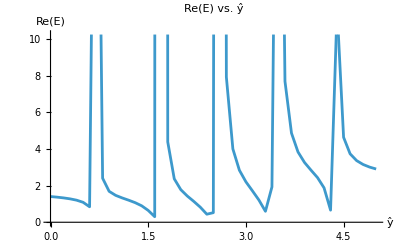

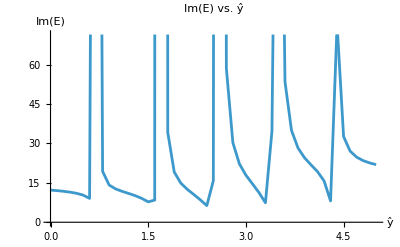

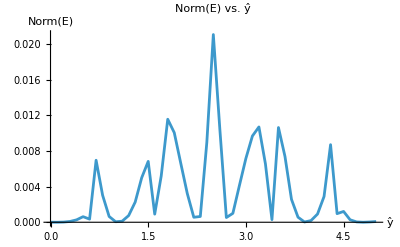

```mathematica
yHatArray=Range[0,5,0.1];
Δ2ReArray={};
Δ2ImArray={};
Δ2NormArray={};
For[i=1,i<=Length[yHatArray],i++,
AppendTo[Δ2ReArray,Δ2Re[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->yHatArray[[i]]}];
AppendTo[Δ2ImArray,Δ2Im[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->yHatArray[[i]]}];
AppendTo[Δ2NormArray,Δ2Norm[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->yHatArray[[i]]}];
]

start=AbsoluteTime[];

EReArray={};
EImArray={};
ENormArray={};
For[i=1,i<=Length[Δ2ReArray],i++,
AppendTo[EReArray,NIntegrate[Δ2ReArray[[i]],{κ,0,0.8*π}]];
AppendTo[EImArray,NIntegrate[Δ2ImArray[[i]],{κ,0,0.8*π}]];
AppendTo[ENormArray,NIntegrate[Δ2NormArray[[i]],{κ,0,0.8*π}]];
]

end=AbsoluteTime[];
end-start

(*Plot[Interpolation[Transpose@{yHatArray,EReArray}][x],{x,1.8,2.52}]*)

ListPlot[Transpose@{yHatArray,EReArray},Joined->True,PlotLabel->"Re(E) vs. ŷ",AxesLabel->{"ŷ","Re(E)"}]
ListPlot[Transpose@{yHatArray,EImArray},Joined->True,PlotLabel->"Im(E) vs. ŷ",AxesLabel->{"ŷ","Im(E)"}]
ListPlot[Transpose@{yHatArray,ENormArray},Joined->True,PlotLabel->"Norm(E) vs. ŷ",AxesLabel->{"ŷ","Norm(E)"}]
```

```mathematica
(*start=AbsoluteTime[];
ERe=NIntegrate[Δ2Re[κ],{κ,0,0.8*π}(*,Assumptions->{0<r<1,α∈Reals,β∈Reals,a1∈Reals,a2∈Reals,a3∈Reals,yHat∈Reals}*)]
(*EIm=Integrate[Δ2Im[κ],{κ,0,r*π},Assumptions->0<r<1]*)
end=AbsoluteTime[];
end-start*)
```

### Node 1

```mathematica
𝔸[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ[κ_]=a10+a21 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBarRe[κ_]=(𝔸[κ]*𝔻[κ]-𝔹[κ]*ℂ[κ])/((𝔸[κ])^2+(𝔹[κ])^2);
κBarIm[κ_]=(-𝔸[κ]*ℂ[κ]-𝔹[κ]*𝔻[κ])/((𝔸[κ])^2+(𝔹[κ])^2);
κBarNorm[κ_]=Abs[κBarRe[κ]+I*κBarIm[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*(𝔸[κ])^2+(𝔹[κ])^2-(𝔸[κ]*𝔻[κ]-𝔹[κ]*ℂ[κ]))^2;
Δ2Im[κ_]=(κ*(𝔸[κ])^2+(𝔹[κ])^2-(-𝔸[κ]*ℂ[κ]-𝔹[κ]*𝔻[κ]))^2;
Δ2Norm[κ_]=(κ-κBarNorm[κ])^2;
```

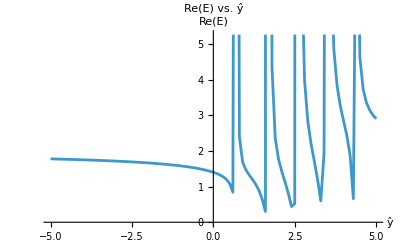

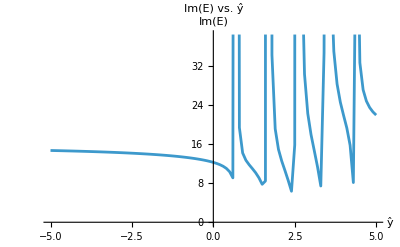

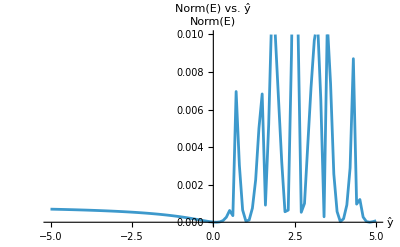

Evaluation time: 14.376886

```mathematica
start=AbsoluteTime[];

yHatArray=Range[-5,5,0.1];
Δ2ReArray={};
Δ2ImArray={};
Δ2NormArray={};
For[i=1,i<=Length[yHatArray],i++,
AppendTo[Δ2ReArray,Δ2Re[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->yHatArray[[i]]}];
AppendTo[Δ2ImArray,Δ2Im[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->yHatArray[[i]]}];
AppendTo[Δ2NormArray,Δ2Norm[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->yHatArray[[i]]}];
]
EReArray={};
EImArray={};
ENormArray={};
For[i=1,i<=Length[Δ2ReArray],i++,
AppendTo[EReArray,NIntegrate[Δ2ReArray[[i]],{κ,0,0.8*π}]];
AppendTo[EImArray,NIntegrate[Δ2ImArray[[i]],{κ,0,0.8*π}]];
AppendTo[ENormArray,NIntegrate[Δ2NormArray[[i]],{κ,0,0.8*π}]];
]

ListPlot[Transpose@{yHatArray,EReArray},Joined->True,PlotLabel->"Re(E) vs. ŷ",AxesLabel->{"ŷ","Re(E)"}]
ListPlot[Transpose@{yHatArray,EImArray},Joined->True,PlotLabel->"Im(E) vs. ŷ",AxesLabel->{"ŷ","Im(E)"}]
ListPlot[Transpose@{yHatArray,ENormArray},Joined->True,PlotLabel->"Norm(E) vs. ŷ",AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸[κ_]=γ00+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBarRe[κ_]=(𝔸[κ]*𝔻[κ]-𝔹[κ]*ℂ[κ])/((𝔸[κ])^2+(𝔹[κ])^2);
κBarIm[κ_]=(-𝔸[κ]*ℂ[κ]-𝔹[κ]*𝔻[κ])/((𝔸[κ])^2+(𝔹[κ])^2);
κBarNorm[κ_]=Abs[κBarRe[κ]+I*κBarIm[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*(𝔸[κ])^2+(𝔹[κ])^2-(𝔸[κ]*𝔻[κ]-𝔹[κ]*ℂ[κ]))^2;
Δ2Im[κ_]=(κ*(𝔸[κ])^2+(𝔹[κ])^2-(-𝔸[κ]*ℂ[κ]-𝔹[κ]*𝔻[κ]))^2;
Δ2Norm[κ_]=(κ-κBarNorm[κ])^2;
```

```mathematica
start=AbsoluteTime[];

yHatArray=Range[-5,5,0.1];
Δ2ReArray={};
Δ2ImArray={};
Δ2NormArray={};
For[i=1,i<=Length[yHatArray],i++,
AppendTo[Δ2ReArray,Δ2Re[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->yHatArray[[i]]}];
AppendTo[Δ2ImArray,Δ2Im[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->yHatArray[[i]]}];
AppendTo[Δ2NormArray,Δ2Norm[κ]/.{α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,yHat->yHatArray[[i]]}];
]
EReArray={};
EImArray={};
ENormArray={};
For[i=1,i<=Length[Δ2ReArray],i++,
AppendTo[EReArray,NIntegrate[Δ2ReArray[[i]],{κ,0,0.8*π}]];
AppendTo[EImArray,NIntegrate[Δ2ImArray[[i]],{κ,0,0.8*π}]];
AppendTo[ENormArray,NIntegrate[Δ2NormArray[[i]],{κ,0,0.8*π}]];
]

ListPlot[Transpose@{yHatArray,EReArray},Joined->True,PlotLabel->"Re(E) vs. ŷ",AxesLabel->{"ŷ","Re(E)"}]
ListPlot[Transpose@{yHatArray,EImArray},Joined->True,PlotLabel->"Im(E) vs. ŷ",AxesLabel->{"ŷ","Im(E)"}]
ListPlot[Transpose@{yHatArray,ENormArray},Joined->True,PlotLabel->"Norm(E) vs. ŷ",AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```